```mathematica
Quit[];
```

## EFT of sub-GeV DM, pseudoscalar mediator

### Setup

```mathematica
$FeynRulesPath=SetDirectory[$UserBaseDirectory<>"/Applications/FeynRules"];
FR$Parallel=False;
<<FeynRules`;
SetDirectory[NotebookDirectory[]];

su2Subs={km->0,kmbar->0,k0->0,k0bar->0,eta->0,etap->0,T->0};
modelName="EFT_MeV_DM_pseudoscalar";
LoadModel[modelName<>".fr"];
```

- FeynRules -

Version: 2.3.31 ( 26 January 2018).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

This model implementation was created by

Adam Coogan

Logan Morrison

Model Version: 1

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model EFT_subGeV_DM_P loaded.

### Write model file

```mathematica
Lag=L;
```

```mathematica
WriteFeynArtsOutput[Lag, MaxParticles->5,Output->modelName]
```

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2013

Counterterms: B. Fuks, 2012

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Neglecting all terms with more than 5 particles.

Collecting the different structures that enter the vertex.

77 possible non-zero vertices have been found -> starting the computation:  / 77.

77 vertices obtained.

Writing FeynArts model file into directory EFT_MeV_DM_pseudoscalar

Writing FeynArts generic file on EFT_MeV_DM_pseudoscalar.gen.

```mathematica
Beep[]
```

```mathematica
newModelDir=NotebookDirectory[]<>modelName
targetDir="/Users/acoogan/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/"<>modelName
```

/Users/acoogan/Physics research/Sub-GeV DM EFT calcs/FeynRules models/EFT of MeV DM/Pseudoscalar mediator/EFT_MeV_DM_pseudoscalar

/Users/acoogan/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/EFT_MeV_DM_pseudoscalar

```mathematica
DeleteDirectory[targetDir,DeleteContents->True];
CopyDirectory[newModelDir,targetDir];
```

### Working to quadratic order in P

#### Looking at P’s potential

Thankfully, P does not acquire a vev!

```mathematica
(b fπ^2)/2 Tr[(QuarkMassMatrix-ⅈ PCouplingMatrix p)Exp[-ⅈ gpGG p/vh]+(QuarkMassMatrix+ⅈ PCouplingMatrix p)Exp[ⅈ gpGG p/vh]]//Series[#,{p,0,4}]&;
%//Simplify
```

b fπ^2 (ComposedChar(m,d)+ComposedChar(m,s)+ComposedChar(m,u))-1/(2 (ComposedChar(v,H))^2)p^2 (b fπ^2 ComposedChar(g,PGG) (ComposedChar(g,PGG) (ComposedChar(m,d)+ComposedChar(m,s)+ComposedChar(m,u))+2 ComposedChar(v,H) (ComposedChar(g,Pdd)+ComposedChar(g,Pss)+ComposedChar(g,Puu))))+1/(24 (ComposedChar(v,H))^4)b fπ^2 p^4 (ComposedChar(g,PGG))^3 (ComposedChar(g,PGG) (ComposedChar(m,d)+ComposedChar(m,s)+ComposedChar(m,u))+4 ComposedChar(v,H) (ComposedChar(g,Pdd)+ComposedChar(g,Pss)+ComposedChar(g,Puu)))+O(p^5)

```mathematica
-(b fπ^2)/2((tr[mm]-ⅈ tr[gpq] p)Exp[-ⅈ gpG p/vh]+(tr[mm]+ⅈ tr[gpq] p)Exp[ⅈ gpG p/vh])//ExpToTrig//Simplify
```

b fπ^2 (p tr(gpq) sin((gpG p)/(ComposedChar(v,H)))-tr(mm) cos((gpG p)/(ComposedChar(v,H))))

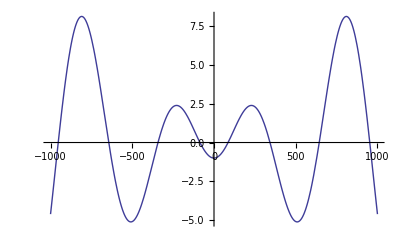

```mathematica
Plot[-(Cos[x/100]-x/100 Sin[x/100]),{x,-1000,1000}]
```

#### Examining mixing with π^0

Mixing term. If we adopt MFV by requiring g_Pq=g_Pf m_q/v, the mixing is proportional to the difference between the up and down Yukawas and can be neglected.

```mathematica
fpi pi0t(Lag//Coefficient[#,pi0t]&//Coefficient[#,fpi,1]&//Simplify)/.{vh->v,b0->B0,gpGG->gPG,muq->mup,mdq->mdown,gpuu->gPU,gpdd->gPD,fpi->fπ}//Apart
```

-B0 fπ pi0t pt (gPD-gPU)-(B0 fπ gPG pi0t pt (mdown-mup))/v

Decompose the mass matrix

```mathematica
mixingSub={eps->B0 fπ (gPu-gPd+(mU-mD)/vH gPG)};
```

```mathematica
massMat={{mπ0^2,-eps},{-eps,mp^2}};
```

```mathematica
{evs,evecs}=Eigensystem[massMat];
```

```mathematica
normdEvecs={evecs⟦1⟧/(√((evecs⟦1⟧⟦1⟧)^2+(evecs⟦1⟧⟦2⟧)^2)),evecs⟦2⟧/(√((evecs⟦2⟧⟦1⟧)^2+(evecs⟦2⟧⟦2⟧)^2))}//FullSimplify;
```

```mathematica
(massMat.normdEvecs⟦1⟧)/evs⟦1⟧-normdEvecs⟦1⟧//Simplify
(massMat.normdEvecs⟦2⟧)/evs⟦2⟧-normdEvecs⟦2⟧//Simplify

Transpose[normdEvecs].DiagonalMatrix[evs].normdEvecs//Simplify
```

{0,0}

{0,0}

(mπ0^2 | -eps
-eps | mp^2)

Assume the mixing angle is small

```mathematica
evs//Series[#,{eps,0,2}]&//FullSimplify[#,Assumptions->{mp>mπ0>0}]&//Normal
{evs⟦2⟧,evs⟦1⟧}//Series[#,{eps,0,2}]&//FullSimplify[#,Assumptions->{0<mp<mπ0}]&//Normal
```

{eps^2/(mπ0^2-mp^2)+mπ0^2,eps^2/(mp^2-mπ0^2)+mp^2}

{eps^2/(mπ0^2-mp^2)+mπ0^2,eps^2/(mp^2-mπ0^2)+mp^2}

```mathematica
evecs//Series[#,{eps,0,2}]&//FullSimplify[#,Assumptions->{mp>mπ0>0}]&//Normal;
{(%⟦1⟧)/(√((%⟦1⟧⟦1⟧)^2+(%⟦1⟧⟦2⟧)^2)),(%⟦2⟧)/(√((%⟦2⟧⟦1⟧)^2+(%⟦2⟧⟦2⟧)^2))}//Series[#,{eps,0,2}]&//FullSimplify[#,Assumptions->{mp>mπ0>0}]&//Normal

evecs//Series[#,{eps,0,2}]&//FullSimplify[#,Assumptions->{0<mp<mπ0}]&//Normal;
{-(%⟦2⟧)/(√((%⟦2⟧⟦1⟧)^2+(%⟦2⟧⟦2⟧)^2)),(%⟦1⟧)/(√((%⟦1⟧⟦1⟧)^2+(%⟦1⟧⟦2⟧)^2))}//Series[#,{eps,0,2}]&//FullSimplify[#,Assumptions->{0<mp<mπ0}]&//Normal
```

(1-eps^2/(2 (mp^2-mπ0^2)^2) | eps/(mp^2-mπ0^2)
eps/(mπ0^2-mp^2) | 1-eps^2/(2 (mp^2-mπ0^2)^2))

(1-eps^2/(2 (mp^2-mπ0^2)^2) | eps/(mp^2-mπ0^2)
eps/(mπ0^2-mp^2) | 1-eps^2/(2 (mp^2-mπ0^2)^2))

Redo calculation to handle the mpi0=mp case:

```mathematica
mixingSub={eps->B0 fπ (gPu-gPd+(mU-mD)/vH gPG)};
```

```mathematica
massMat={{mπ0^2,-eps},{-eps,mπ0^2}};
```

```mathematica
{evs,evecs}=Eigensystem[massMat];
```

```mathematica
normdEvecs={evecs⟦1⟧/(√((evecs⟦1⟧⟦1⟧)^2+(evecs⟦1⟧⟦2⟧)^2)),evecs⟦2⟧/(√((evecs⟦2⟧⟦1⟧)^2+(evecs⟦2⟧⟦2⟧)^2))}//FullSimplify;
```

```mathematica
(massMat.normdEvecs⟦1⟧)/evs⟦1⟧-normdEvecs⟦1⟧//Simplify
(massMat.normdEvecs⟦2⟧)/evs⟦2⟧-normdEvecs⟦2⟧//Simplify

Transpose[normdEvecs].DiagonalMatrix[evs].normdEvecs//Simplify
```

{0,0}

{0,0}

(mπ0^2 | -eps
-eps | mπ0^2)

```mathematica
evs
```

{mπ0^2-eps,eps+mπ0^2}

```mathematica
{{π0},{pp}}=normdEvecs.{{π0t},{ppt}}//Simplify
```

((ppt+π0t)/(√2)
(ppt-π0t)/(√2))

Not sure how to interpret this. π0 gets the same coupling to DM as P. P gets the same couplings to everything as π0.

### Full analysis of V(P,π^0)

With g_(P q)s set to zero, the potential is

```mathematica
axionPotential=-B0 f^2(mu Cos[π0/f-gG p/v]+md Cos[π0/f+gG p/v]);
axionPotential=-B0(mu+md) f^2 √(1-(4mu md)/(mu+md)^2 Sin[b]^2)Cos[a-ϕ]/.{ϕ->ArcTan[(mu-md)/(mu+md)Tan[b]]}/.{a->π0/f,b->gG p/v}
```

-B0 f^2 (md+mu) √(1-(4 md mu sin^2((gG p)/v))/(md+mu)^2) cos(π0/f-tan^-1(((mu-md) tan((gG p)/v))/(md+mu)))

Easy to find that ⟨p⟩=0:

```mathematica
vπ0AxPotSub=Solve[D[axionPotential,π0]==0,π0]⟦1⟧;

axionPotential/.vπ0AxPotSub//Simplify
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

-B0 f^2 (md+mu) √(1-(4 md mu sin^2((gG p)/v))/(md+mu)^2)

With nonzero coupling to quarks:

```mathematica
potential=-B0 f^2(mu Cos[π0/f-gG p/v]+md Cos[π0/f+gG p/v]+gpu p Sin[π0/f-gG p/v]-gpd p Sin[π0/f+gG p/v]);

potential=1/2 mpt^2 p^2+axionPotential-B0 f^2(Abs[gd-gu] √(1+(4 gu gd)/(gd-gu)^2 Sin[b]^2)p Sin[a+ArcTan[ϕ]])/.{ϕ->ArcTan[(gu+gd)/(gd-gu)Tan[b]]}/.{a->π0/f,b->gG p/v};
```

Expand to 𝒪(p^2/v^2), since that’s what was done in the microscopic model:

```mathematica
potExpanded=potential//Series[#,{p,0,2}]&//Simplify//Normal;
```

P^2 term’s coefficient must be its mass:

```mathematica
mptSub=Solve[D[potExpanded/.π0->0,{p,2}]==mp^2,mpt]⟦2⟧//FullSimplify
```

{mpt→(√(2 B0 f^2 gG v (gd+gu) Abs[gd-gu]+(gd-gu) (mp^2 v^2-B0 f^2 gG^2 (md+mu))))/(√(v^2 (gd-gu)))}

```mathematica
$Assumptions={mu>0,md>0,gu∈Reals,gd∈Reals,v>0,0≤π0<2π f,mp>0,B0>0,f>0};
```

Can solve for ⟨π^0⟩ in terms of P’s vev. Substituting this back in, we see that P’s vev is 0, and thus ⟨π^0⟩=0 as well.

```mathematica
π0Subs=D[potExpanded,π0]==0//Solve[{#},π0]&;

potExpanded/.π0Subs/.mptSub//Series[#,{p,0,2}]&//Simplify//Normal

π0Subs/.p->0//Simplify
```

{Piecewise[{{(p^2 (mp^2 (md+mu) v^2-B0 f^2 (gG (md-mu)+(gu-gd) v)^2))/(2 (md+mu) v^2)-B0 f^2 (md+mu), gd≥gu}, {B0 (md+mu) f^2+(p^2 (mp^2 (md+mu) v^2-B0 f^2 ((md^2+6 mu md+mu^2) gG^2+2 (gd md+3 gu md+3 gd mu+gu mu) v gG-(gd-gu)^2 v^2)))/(2 (md+mu) v^2), True}}],Piecewise[{{B0 (md+mu) f^2+(p^2 (B0 (-(md^2+6 mu md+mu^2) gG^2+2 (gd md+3 gu md+3 gd mu+gu mu) v gG+(gd-gu)^2 v^2) f^2+mp^2 (md+mu) v^2))/(2 (md+mu) v^2), gd≥gu}, {(p^2 (mp^2 (md+mu) v^2-B0 f^2 (gG (md-mu)+(gd-gu) v)^2))/(2 (md+mu) v^2)-B0 f^2 (md+mu), True}}]}

{{π0→ConditionalExpression[f (tan^-1(gd-gu,0)+2 π c_1),c_1∈ℤ]},{π0→ConditionalExpression[f (tan^-1(gu-gd,0)+2 π c_1),c_1∈ℤ]}}

```mathematica
mpt^2/.mptSub//FullSimplify;
%-mp^2/.B0->mΠ^2/(mu+md)//FullSimplify
```

(f^2 gG mΠ^2 (2 v (gd+gu)-gG (md+mu) sgn(gd-gu)))/(v^2 (md+mu) sgn(gd-gu))

```mathematica
fpi pi0t(Lag//Coefficient[#,pi0t]&//Coefficient[#,fpi,1]&//Simplify)/.{vh->v,b0->B0,gpGG->gPG,muq->mup,mdq->mdown,gpuu->gPU,gpdd->gPD,fpi->fπ}//Apart
```

-B0 fπ pi0t pt (gPD-gPU)-(B0 fπ gPG pi0t pt (mdown-mup))/v

```mathematica
potExpanded//Series[#,{π0,0,2}]&//Simplify//Normal;
π0 p (%//Coefficient[#,π0]&//Coefficient[#,p]&)//Apart
```

(B0 f gG p π0 (md-mu))/v-B0 f p π0 Abs[gd-gu]

```mathematica
potential
```

-B0 f^2 p Abs[gd-gu] √((4 gd gu sin^2((gG p)/v))/(gd-gu)^2+1) sin(π0/f+tan^-1(tan^-1(((gd+gu) tan((gG p)/v))/(gd-gu))))-B0 f^2 (md+mu) √(1-(4 md mu sin^2((gG p)/v))/(md+mu)^2) cos(π0/f-tan^-1(((mu-md) tan((gG p)/v))/(md+mu)))+(mpt^2 p^2)/2

```mathematica
-B0 f^2(mu Cos[π0/f-gG p/v]+md Cos[π0/f+gG p/v]+gpu p Sin[π0/f-gG p/v]-gpd p Sin[π0/f+gG p/v])

%//Series[#,{p,0,2}]&//Series[#,{π0,0,2}]&//Simplify//Normal;
π0 p (%//Coefficient[#,π0]&//Coefficient[#,p]&//FullSimplify)//Apart
```

-B0 f^2 (-gpd p sin(π0/f+(gG p)/v)-gpu p sin((gG p)/v-π0/f)+md cos(π0/f+(gG p)/v)+mu cos((gG p)/v-π0/f))

(B0 f p π0 (gG md-gG mu+gpd v-gpu v))/v